```mathematica
(* Notation:
ep, em; fp, fm = number of each type of electron up/down (e = ej and f = ei)
np, nm = number of nuclei up/down
et, ft, nt = total number of each electron/nuclei *)
```

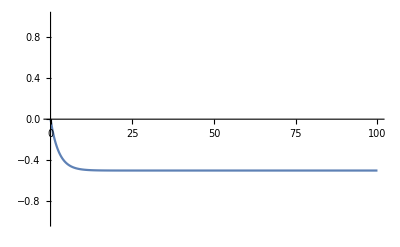

```mathematica
(* A test of the solid effect model given in Wenkebach for comparison *)
ClearAll["Global`*"];
subs={nt->np[t]+nm[t],et->ep[t]+em[t],w->0.2};
solidEffectEqns={ep'[t]==-w/nt(ep[t]nm[t]-em[t]np[t]),
em'[t]==w/nt(ep[t]nm[t]-em[t]np[t]),
np'[t]==w/et(ep[t]nm[t]-em[t]np[t]),
nm'[t]==-w/et(ep[t]nm[t]-em[t]np[t]),
ep[0]==0,em[0]==1,np[0]==1/2,nm[0]==1/2};
sol=NDSolve[solidEffectEqns/.subs,{em,ep,nm,np},{t,0,1000}];
Plot[(np[t]-nm[t])/(np[t]+nm[t])/.sol,{t,0,100},PlotRange->{{0,100},{-1,1}}]
```

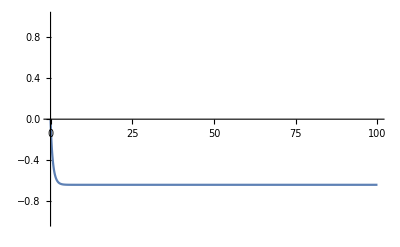

```mathematica
(* The thermal mixing model given in Wenkebach *)
ClearAll["Global`*"];
subs={nt->np[t]+nm[t],et->ep[t]+em[t],ft->fp[t]+fm[t]};
(* Parameters to change:
* Below, you can change the value of w (Subscript[W, tm]^+).
* peInit, pfInit, and pnInit are the initial polarizations of the two types of electrons and the nuclei, respectively.
* ce and cf are the ratios of the number of each type of electron to the number of nuclei (the analogue to the constant C in the solid effect).
*)
initial={w->1,peInit->1,pfInit->-1,pnInit->0};
constants={ce->1*^-4,cf->1*^-4};
thermalMixingEqns={ep'[t]==w/(ft nt)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
em'[t]==-w/(ft nt)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
fp'[t]==-w/(et nt)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
fm'[t]==w/(et nt)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
np'[t]==w/(et ft)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
nm'[t]==-w/(et ft)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
ep[0]==(ce(1+peInit))/2,em[0]==(ce(1-peInit))/2,
fp[0]==(cf(1+pfInit))/2,fm[0]==(cf(1-pfInit))/2,
np[0]==(1+pnInit)/2,nm[0]==(1-pnInit)/2};
sol=NDSolve[thermalMixingEqns/.subs/.initial/.constants,{em,ep,fm,fp,nm,np},{t,0,1000}];
Plot[(np[t]-nm[t])/(np[t]+nm[t])/.sol,{t,0,100},PlotRange->{{0,100},{-1,1}}]
```

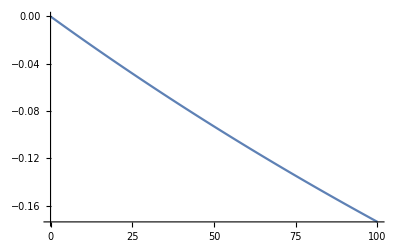

```mathematica
(* The thermal mixing model given in Wenkebach, but with C parameters correctly(?) used *)
ClearAll["Global`*"];
subs={nt->np[t]+nm[t],et->ep[t]+em[t],ft->fp[t]+fm[t]};
(* Parameters to change:
* Below, you can change the value of w (Subscript[W, tm]^+).
* peInit, pfInit, and pnInit are the initial polarizations of the two types of electrons and the nuclei, respectively.
* ce and cf are the ratios of the number of each type of electron to the number of nuclei (the analogue to the constant C in the solid effect).
*)
initial={w->10,peInit->1,pfInit->-1,pnInit->0};
constants={ce->1*^-4,cf->1*^-4};
thermalMixingEqns={ep'[t]==(w (cf))/(ft nt)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
em'[t]==(-w (cf))/(ft nt)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
fp'[t]==(-w (ce))/(et nt)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
fm'[t]==(w (ce))/(et nt)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
np'[t]==(w (ce+cf))/(et ft)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
nm'[t]==(-w(ce+cf))/(et ft)(em[t]fp[t]nm[t]-ep[t]fm[t]np[t]),
ep[0]==(ce(1+peInit))/2,em[0]==(ce(1-peInit))/2,
fp[0]==(cf(1+pfInit))/2,fm[0]==(cf(1-pfInit))/2,
np[0]==(1+pnInit)/2,nm[0]==(1-pnInit)/2};
sol=NDSolve[thermalMixingEqns/.subs/.initial/.constants,{em,ep,fm,fp,nm,np},{t,0,10000}];
Plot[(np[t]-nm[t])/(np[t]+nm[t])/.sol,{t,0,100},PlotRange->Full]
```